```mathematica
Obtaining Surface of Revolution of Curves
```

```mathematica
Obtain the surface of revolution of parabola y^2=4ax.
Solution:
```

```mathematica
RevolutionPlot3D[{t^2,2t},{t,-2,2},AxesLabel->{x,y,z},RevolutionAxis->{0,0,1},PlotStyle->Green,AxesStyle->Blue,Background->White]
```

```mathematica
Obtain the surface of revolution of hyperbola x^2/9-y^2/4=1.
Solution:
```

```mathematica
RevolutionPlot3D[{3Cosh[t],2Sinh[t]},{t,-Pi,Pi},AxesLabel->{x,y,z},RevolutionAxis->{0,0,1},PlotStyle->Brown, Background->Orange]
```

-Graphics3D-

```mathematica
Obtain surface of revolution of ellipse.
Solution:
```

```mathematica
RevolutionPlot3D[{4Cos[t],2Sin[t]},{t,-Pi,Pi},AxesLabel->{x,y,z},RevolutionAxis->{0,0,1},PlotStyle->Yellow,AxesStyle->Blue,Background->Purple]
```

-Graphics3D-

```mathematica
Torus ( or Donut)
Solution:
```

```mathematica
RevolutionPlot3D[{2+Cos[t],Sin[t]},{t,-2Pi,Pi},AxesLabel->{x,y,z},AxesStyle->Green]
```

-Graphics3D-

```mathematica
Obtain surface of revolution of curves Sinx,Cosx,Tanx.
Solution:
```

```mathematica
Sinx
```

```mathematica
RevolutionPlot3D[Sin[x],{x,0,Pi},AxesLabel->{"x Axis","y Axis","z Axis"},RevolutionAxis->{0,0,1},PlotStyle->White,MeshFunctions->{#3&},MeshStyle->Dotted,AxesStyle->Red,Background->Blue]
```

-Graphics3D-

```mathematica
Cosx
```

```mathematica
RevolutionPlot3D[Cos[x],{x,0,Pi},AxesLabel->{"x Axis","y Axis","z Axis"},RevolutionAxis->{0,0,1},PlotStyle->White,AxesStyle->Red,Background->Blue]
```

-Graphics3D-

```mathematica
Tanx
```

```mathematica
RevolutionPlot3D[Tan[x],{x,0,Pi},AxesLabel->{"x Axis","y Axis","z Axis"},RevolutionAxis->{0,0,1},PlotStyle->White,AxesStyle->Red,Background->Blue]
```

-Graphics3D-

```mathematica
Drawing the surface and finding its level curves from the given height
```

```mathematica
Equation:   f(x)=x^2-y^2
```

```mathematica
Plot3D[x^2-y^2,{x,-5,5},{y,-5,5},Mesh->All,MeshFunctions->(#3&)]
```

-Graphics3D-

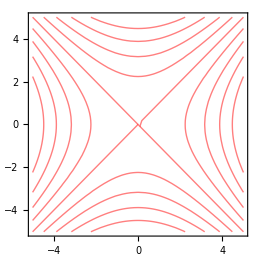

```mathematica
ContourPlot[x^2-y^2,{x,-5,5},{y,-5,5},ContourShading-> False,ContourStyle->{{Thick,Red}}]
```

```mathematica
Equation:   f(x)=Sin √(x^2+y^2)
```

```mathematica
Plot3D[Sin[√(x^2+y^2)],{x,-5,5},{y,-5,5},MeshFunctions->(#3&),BoxRatios->{2,2,2},MeshStyle->{Thick,Red}]
```

-Graphics3D-

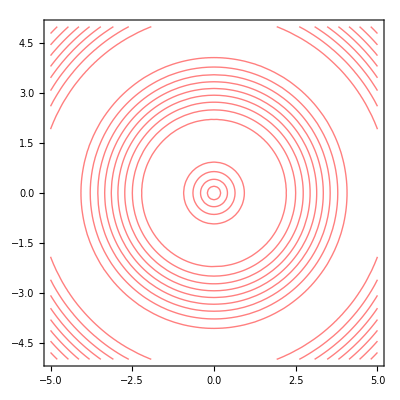

```mathematica
ContourPlot[Sin[√(x^2+y^2)],{x,-5,5},{y,-5,5},ContourShading-> False,ContourStyle->{{Thick,Red}}]
```

```mathematica
Heat Equation
```

```mathematica
Equation:   (∂U[X,T])/(∂T) - (∂^2 U[X,T])/(∂X^2)=0 ,U[X,0]=x^2-x ,U[0,t]=0,   u[l,t]=0,   0<x<l  l=1
```

```mathematica
heqn1={D[u[x,t],t]-D[u[x,t],x,x]==0,u[x,0]==x^2-x,u[0,t]==0,u[1,t]==0};
sol1=u[x,t]/.NDSolve[heqn1,u[x,t],{x,0,1},{t,0,1}]
Plot3D[sol1,{x,0,1},{t,0,1},ColorFunction->Hue,AxesLabel->{"x axis","y axis","u[x,t]"}]
```

{InterpolatingFunction[…][x,t]}

-Graphics3D-

```mathematica
Wave Equation
```

```mathematica
Equation:   (∂^2 U[X,T])/(∂T^2)-4(∂^2 U[X,T])/(∂X^2)=0,U[X,0]=0,Subscript[U, t][X,0]=X[1-X],U[0,T]=0,U[1,T]=0
```

```mathematica
weqn2={D[u[x,t],t,t]-4D[u[x,t],x,x]==0,u[x,0]==0,u[0,t]==0,u[1,t]==0,Derivative[0,1][u][x,0]==x(1-x)}
sol2=u[x,t]/.NDSolve[weqn2,u[x,t],{x,0,1},{t,0,1}]
Plot3D[sol2,{x,0,1},{t,0,1},AxesLabel->{"x axes","y axes","u[x,t]"},AxesOrigin->{0,0},ColorFunction->Hue]
```

{u^(0,2)[x,t]-4 u^(2,0)[x,t]==0,u[x,0]==0,u[0,t]==0,u[1,t]==0,u^(0,1)[x,0]==(1-x) x}

{InterpolatingFunction[…][x,t]}

-Graphics3D-

```mathematica
Growth Model (Exponential Case )
```

Exponential Growth : -
If a function x(t) grows continuously at a rate k>0, then x(t) has the form
                                                                                     x(t)=x_0 e^kt    
    where x_0 is the initial amount and t is the time. In this case , the quantity x(t) is said to exhibit exponential growth, and k is the growth rate. It’s differential model is given by 2%
                                                               dx/dt=kx , k>0

```mathematica
Suppose that the population of a certain country grows at an annual rate of 2%.If the current population is 3 million, what will the population be in 10 years? Also plot the graph of the solution.

Solution : Here Subscript[x, O]=3,k=2%=0.02,t=10 years, x[t]=?
```

{{x[t]→ⅇ^(k t) C[1]}}

3 ⅇ^(0.02 t)

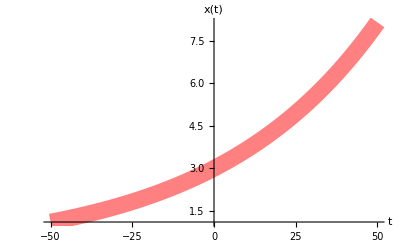

3.66421

```mathematica
Sol=DSolve[x'[t]==k x[t],x[t],t]
Sol1=Evaluate[x[t]/.Sol[[1]]/.{k->0.02,C[1]->3}]
Plot[Sol1,{t,-50,50},PlotStyle->{Pink,Thickness[0.03]},AxesLabel->{t,x[t]},AxesStyle->Arrowheads[{-.03,.03}]]
x[10]=Evaluate[Sol1/.{t->10}]
```

```mathematica
Conclusion: Hence population after 10 years will be 3.66421.
```

```mathematica
Decay Model (Exponential Case)

Exponential Decay:
If a function x(t) decreases continuously at a rate k>0, then x(t) has the form   
                                                                                 x(t)=Subscript[x, O] e^-kt
where Subscript[x, O] is the initial amount Subscript[x, O]. In this case, the quantity x(t) is said to exhibit exponential decay, and k is the decay rate. It's differential model is given by dx/dt=-kx , k>0.
```

```mathematica
Suppose that a certain radioactive element has an annual decay rate of 10%. Starting with a 200 gram sample of the element , how many grams will be left in 3 years?
Solution:Here k=10%=0.1,Subscript[x, O]=200,t=3,x(t)=?
```

{{x[t]→ⅇ^(-k t) C[1]}}

200 ⅇ^(-0.1 t)

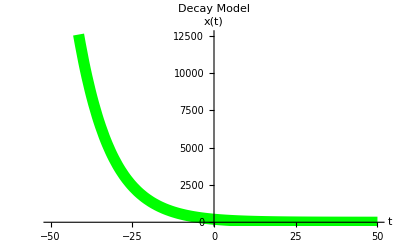

148.164

```mathematica
Sol=DSolve[x'[t]==-k x[t],x[t],t]
Sol1=Evaluate[x[t]/.Sol[[1]]/.{k->0.1,C[1]->200}]
Plot[Sol1,{t,-50,50},PlotStyle->{Green,Thickness[0.02]},AxesLabel->{t,x[t]},AxesStyle->Arrowheads[{-.03,.03}],PlotLabel->"Decay Model"]
x[3]=Evaluate[Sol1/.{t->3}]
```

```mathematica
Conclusion: Hence 148.164gms of radioactive element will be left after 3 years.
```